```mathematica
Hypergeometric1F1[a,b,c]
```

Hypergeometric1F1[a,b,c]

```mathematica
Assuming[a>0,Gamma[1-I*x]]
```

Gamma[1-ⅈ x]

```mathematica
Gamma[2]
```

1

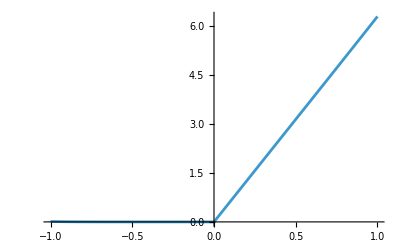

```mathematica
Plot[Exp[Pi/k]*Abs[Gamma[1-I/k]]^2*k^2,{k,-1,1}]
```

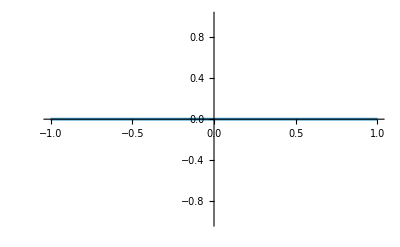

```mathematica
Plot[Sinh[k]/k-Sinh[-k]/(-k),{k,-1,1}]
```

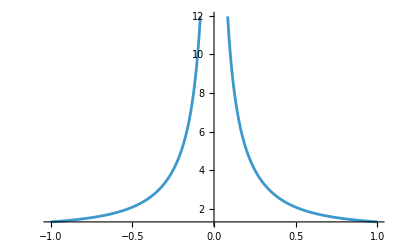

```mathematica
Plot[1/k*Coth[1/k],{k,-1,1}]
```

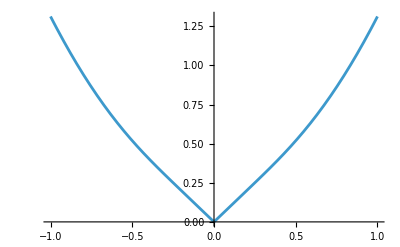

```mathematica
Plot[q*Coth[1/q],{q,-1,1}]
```

Coth[1/q]+Csch[1/q]^2/q

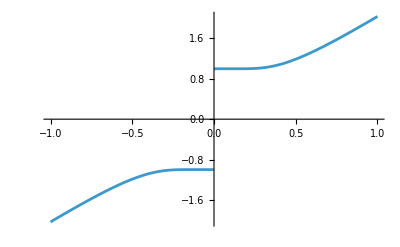

```mathematica
D[q*Coth[1/q],q]
Plot[%,{q,-1,1}]
```

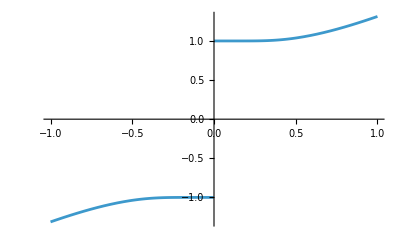

```mathematica
Plot[Coth[1/k],{k,-1,1}]
```

```mathematica
k*Coth[1/k]
```

```mathematica
Series[Coth[x],{x,0,4}]
```

1/x+x/3-x^3/45+O[x]^5

```mathematica
Series[Log[1/x],{x,0,1}]
```

Log[1/x]+O[x]^2

```mathematica
ComplexPlot3D[Log[k],{k,-1-1*I,1+1*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[k*Coth[1/k],{k,-1-1*I,1+1*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[(z^2+1)/(z^2-1),{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg"]
```

```mathematica
Normal[Series[1/z*Coth[z],{z,0,10}]]
%//.{z->1/q}
```

1/3+1/z^2-z^2/45+(2 z^4)/945-z^6/4725+(2 z^8)/93555-(1382 z^10)/638512875

1/3-1382/(638512875 q^10)+2/(93555 q^8)-1/(4725 q^6)+2/(945 q^4)-1/(45 q^2)+q^2

```mathematica
D[z*Coth[1/z],z]
ComplexPlot3D[%,{z,-0.5-0.5*I,0.5+0.5*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z},PlotRange->{0,100}]
```

Coth[1/z]+Csch[1/z]^2/z

-Graphics3D-

```mathematica
D[z*Coth[1/z],z]
ComplexPlot3D[%,{z,-0.5-0.5*I,0.5+0.5*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z},PlotRange->{0,10}]
Plot[%%,{z,-1,1}]
```

Coth[1/z]+Csch[1/z]^2/z

-Graphics3D-

-Graphics-

Coth[1/z]+Csch[1/z]^2/z

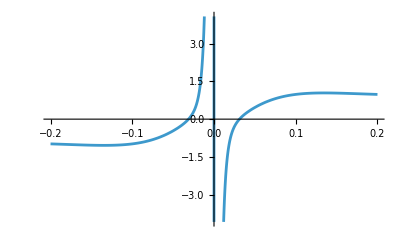

```mathematica
D[z*Coth[1/z],z]
Plot[Re[%//.{z->x+I*0.16}],{x,-0.2,0.2}]
```

```mathematica
Series[z*Coth[1/z],{z,0,3}]
```

Coth[1/z+O[z]^4] (z+O[z]^4)

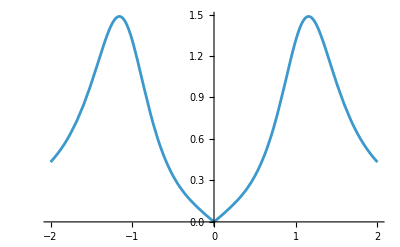

```mathematica
Plot[q*Coth[1/q]/((q^2-1)^2+1),{q,-2,2}]
```

Coth[u]/((1+(-1+1/u^2)^2) u^3)

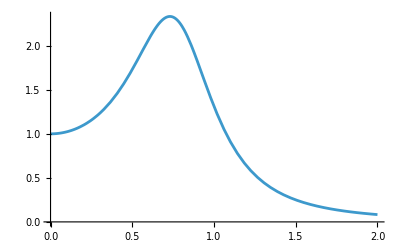

```mathematica
Coth[u]/u^3/(1+(1/u^2-1)^2)
Plot[%,{u,0,2}]
```

```mathematica
Coth[z]/z^3
ComplexPlot3D[%,{z,-1-1*I,1+1*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z}]
```

Coth[z]/z^3

-Graphics3D-

```mathematica
Coth[z]/z^3/(1+(1/z^2-1)^2)
ComplexPlot3D[%,{z,-1-10*I,1+10*I},PlotLegends->Automatic,ColorFunction->"CyclicLogAbsArg",AxesLabel->{Re,Im,z}]
```

Coth[z]/((1+(-1+1/z^2)^2) z^3)

-Graphics3D-

```mathematica
Integrate[1/z^3]
```

Coth[0.1+ⅈ x]/(0.1+ⅈ x)^3

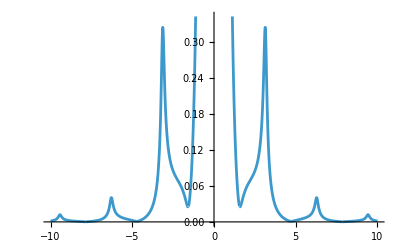

```mathematica
Coth[z]/z^3;
%//.{z->0.1+I*x}
Plot[Abs[%],{x,-10,10}]
```

```mathematica
Coth[z]/z^3/((1-1/z^2)^2+1)
Series[%,{z,0,0}]
```

Coth[z]/((1+(1-1/z^2)^2) z^3)

1+O[z]^1

```mathematica
Assuming[a>0&&c>0&&b∈Reals&&b^2<4*a*c,Integrate[z/(a*z^4-b*z^2+c),{z,0,Infinity}]]
```

(π+2 ArcTan[b/(√(-b^2+4 a c))])/(2 √(-b^2+4 a c))

```mathematica
1/(z*Coth[z])
%//.{z->Pi*I*0}
```

Tanh[z]/z

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
ArcTan[2]
```

ArcTan[2]

```mathematica
-
```

```mathematica
-
```

```mathematica
ArcTan[-10000]
N[%]+Pi/2
```

-ArcTan[10000]

0.0001

```mathematica
?Residue
```

```mathematica
Residue[Coth[z],{z,3*I*Pi}]
```

1

```mathematica
Pi*kappa/Sqrt[2*mt*(En^2+Gammat^2)]*(Sqrt[Sqrt[En^2+Gammat^2]+En]-I*Sqrt[Sqrt[En^2+Gammat^2]-En])
Assuming[Gammat>0&&En∈Reals,Simplify[%^2]]
```

((-ⅈ √(-En+√(En^2+Gammat^2))+√(En+√(En^2+Gammat^2))) kappa π)/(√2 √((En^2+Gammat^2) mt))

(kappa^2 π^2)/(En mt+ⅈ Gammat mt)

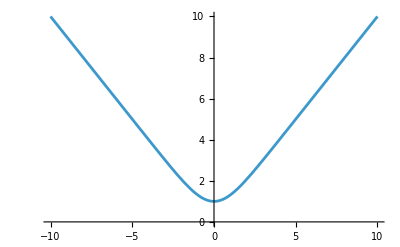

```mathematica
Plot[z*Coth[z],{z,-10,10}]
```

```mathematica
LaguerreL[3,1,0]
```

4

```mathematica
Assuming[n>0,Simplify[(2*kappa/n)^(3/2)*1/(2*n^2)^(1/2)*n]/Sqrt[4*Pi]]
```

(kappa/n)^(3/2)/(√π)

```mathematica
(4*Pi)/(2*Pi)^3
```

1/(2 π^2)

```mathematica
TrigToExp[x+x*Coth[x]]
Simplify[%]
```

x+((ⅇ^-x+ⅇ^x) x)/(-ⅇ^-x+ⅇ^x)

(2 ⅇ^(2 x) x)/(-1+ⅇ^(2 x))

```mathematica
Exp[x]*x/Sinh[x]
Simplify[TrigToExp[%]]
```

ⅇ^x x Csch[x]

(2 ⅇ^(2 x) x)/(-1+ⅇ^(2 x))

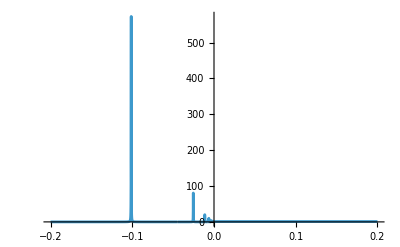

645.031

80.633

7.99959

```mathematica
Re[Coth[1/Sqrt[x-I*0.0001]]];
Plot[%,{x,-0.2,0.2},PlotRange->All]
%%//.{x->-1/Pi^2}
%%%//.{x->-1/Pi^2/4}
%%/%
```

```mathematica
2*z/(z^2+n^2*Pi^2);
Im[z]*0.0001/(0.0001^2);
Sqrt[2]/(n^2*Pi^2)*(Abs[En+I*0.0001]+1/(Pi^2*n^2))/(0.0001^2+(En+1/(Pi^2*n^2))^2)*Sqrt[En+Abs[En+I*0.0001]];
N[Re[%//.{z->1/Sqrt[En-I*0.0001],En->-1/n^2/Pi^2}]];
%//.{n->1}
%%//.{n->2}
%%/%
```

645.031

80.629

7.99999

```mathematica
569/79//N
```

7.20253

```mathematica
D[Log[Sinh[x]],x]
```

Coth[x]

```mathematica
D[Log[x],x]
```

1/x

```mathematica
Simplify[D[Log[1+x^2/(Pi^2*n^2)],x]]
```

(2 x)/(n^2 π^2+x^2)

```mathematica
Sum[1/(z^2+n^2*Pi^2),{n,1,Infinity}]
```

(-1+z Coth[z])/(2 z^2)

```mathematica
Sum[1/n^3/(g^2+(e+k^2/(mt*n^2))^2),{n,1,Infinity}]
```

-1/4 mt RootSum[k^4+2 e k^2 mt+e^2 mt^2+g^2 mt^2+4 e k^2 mt #1+4 e^2 mt^2 #1+4 g^2 mt^2 #1+2 e k^2 mt #1^2+6 e^2 mt^2 #1^2+6 g^2 mt^2 #1^2+4 e^2 mt^2 #1^3+4 g^2 mt^2 #1^3+e^2 mt^2 #1^4+g^2 mt^2 #1^4&,PolyGamma[0,-#1]/(e k^2+e^2 mt+g^2 mt+2 e^2 mt #1+2 g^2 mt #1+e^2 mt #1^2+g^2 mt #1^2)&]

```mathematica
Sum[1/n^3/(e+1/n^2+I*g),{n,1,Infinity}]
```

1/2 (2 EulerGamma+PolyGamma[0,-(-e-√(-e-ⅈ g)-ⅈ g)/(e+ⅈ g)]+PolyGamma[0,-(-e+√(-e-ⅈ g)-ⅈ g)/(e+ⅈ g)])

```mathematica
Sum[1/n^2*1/(e+k/n^2),{n,1,Infinity}]
Assuming[kappa>0&&mt>0&&En>0,Simplify[%//.{e->En,k->kappa^2/mt}]]
Assuming[kappa>0&&mt>0&&En>0,Simplify[TrigToExp[%]]]
```

(-√e+√k π Coth[(√k π)/(√e)])/(2 √e k)

(-mt+kappa √(mt/En) π Coth[(kappa π)/(√(En mt))])/(2 kappa^2)

(mt-ⅇ^((2 kappa π)/(√(En mt))) mt+(1+ⅇ^((2 kappa π)/(√(En mt)))) kappa √(mt/En) π)/(2 (-1+ⅇ^((2 kappa π)/(√(En mt)))) kappa^2)

```mathematica
Simplify[TrigToExp[1+Coth[x]]]
```

(2 ⅇ^(2 x))/(-1+ⅇ^(2 x))

```mathematica
Sum[1/n^2*1/(g^2+(En+k/n^2)^2),{n,1,Infinity}]
Simplify[%]
```

-(ⅈ (-√(-En+ⅈ g) π Cot[(√k π)/(√(-En-ⅈ g))]+√(-En-ⅈ g) π Cot[(√k π)/(√(-En+ⅈ g))]))/(4 √(-En-ⅈ g) √(-En+ⅈ g) g √k)

(ⅈ π (Cot[(√k π)/(√(-En-ⅈ g))]/(√(-En-ⅈ g))-Cot[(√k π)/(√(-En+ⅈ g))]/(√(-En+ⅈ g))))/(4 g √k)

```mathematica
Sum[1/n^3*g/Abs[En+k/n^2+I*g]^2,{n,1,Infinity}]
```

∑_(n=1)^∞ g/(n^3 Abs[En+ⅈ g+k/n^2]^2)

```mathematica
Assuming[g>0&&k>0&&En∈Reals,Sum[1/n^3/(k/n^2-En-I*g),{n,1,Infinity}]]
```

1/(2 k)(2 EulerGamma+PolyGamma[0,-(-En-ⅈ g-√(En k+ⅈ g k))/(En+ⅈ g)]+PolyGamma[0,-(-En-ⅈ g+√(En k+ⅈ g k))/(En+ⅈ g)])

```mathematica
Assuming[g>0&&k>0&&En∈Reals,Sum[1/n^3/(g^2+(1+k^2/n^2)^2),{n,1,Infinity}]]
```

-1/4 RootSum[En^2+g^2+2 En k^2+k^4+4 En^2 #1+4 g^2 #1+4 En k^2 #1+6 En^2 #1^2+6 g^2 #1^2+2 En k^2 #1^2+4 En^2 #1^3+4 g^2 #1^3+En^2 #1^4+g^2 #1^4&,PolyGamma[0,-#1]/(En^2+g^2+En k^2+2 En^2 #1+2 g^2 #1+En^2 #1^2+g^2 #1^2)&]

```mathematica
Sum[k^2/n^4*g/(k/n^2-En-I*g),{n,1,Infinity}];
Simplify[%]
```

1/6 g (-3 En-3 ⅈ g+k π^2+3 √(En+ⅈ g) √k π Cot[(√k π)/(√(En+ⅈ g))])

```mathematica
Sum[k^2/n^4*g/(g^2+(En+k^2/n^2)^2),{n,1,Infinity}];
Simplify[%]
```

(ⅈ (2 ⅈ g+√(-En-ⅈ g) k π Cot[(k π)/(√(-En-ⅈ g))]-√(-En+ⅈ g) k π Cot[(k π)/(√(-En+ⅈ g))]))/(4 k^2)

```mathematica
Sum[1/n^3*1/(-En-kappa^2/(mt*n^2)-I*Gammat),{n,1,Infinity}];
Assuming[kappa>0&&mt>0&&Gammat>0&&En∈Reals,Simplify[Im[%]*kappa^3/(2*Pi)]];
Simplify[%+kappa*mt/4*(1/2+1/Pi*ArcTan[En/Gammat]+Re[Coth[Pi*kappa/Sqrt[mt*(En-I*Gammat)]]])]
tmpMyExpression=Assuming[mt>0,Simplify[%//.{En->xE*mt,Gammat->xΓ*mt,kappa->xKappa*mt}]]
```

(kappa mt (π+2 ArcTan[En/Gammat]-2 Im[PolyGamma[0,(En+ⅈ Gammat-kappa √(-(En+ⅈ Gammat)/mt))/(En+ⅈ Gammat)]+PolyGamma[0,(En+ⅈ Gammat+kappa √(-(En+ⅈ Gammat)/mt))/(En+ⅈ Gammat)]]+2 π Re[Coth[(kappa π)/(√((En-ⅈ Gammat) mt))]]))/(8 π)

(mt^2 xKappa (π+2 ArcTan[xE/xΓ]-2 Im[PolyGamma[0,(xE-xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]+PolyGamma[0,(xE+xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]]+2 π Re[Coth[(π xKappa)/(√(xE-ⅈ xΓ))]]))/(8 π)

```mathematica
Sum[1/n^3*1/(-En-kappa^2/(mt*n^2)-I*Gammat),{n,1,Infinity}];
Assuming[kappa>0&&mt>0&&Gammat>0&&En∈Reals,Simplify[Im[%]*kappa^3/(2*Pi)]];
Simplify[%+kappa*mt/4*(1/2+1/Pi*ArcTan[En/Gammat]+Re[Coth[Pi*kappa/Sqrt[mt*(En-I*Gammat)]]])]
tmpMyExpression=Assuming[mt>0,Simplify[%//.{En->xE*mt,Gammat->xΓ*mt,kappa->xKappa*mt}]]
Sum[1/n^3*1/(-En-kappa^2/(mt*n^2)-I*Gammat),{n,1,1}];
Assuming[kappa>0&&mt>0&&Gammat>0&&En∈Reals,Simplify[Im[%]*kappa^3/(Pi)]];
tmpMyExpression2=Assuming[mt>0,Simplify[%//.{En->xE*mt,Gammat->xΓ*mt,kappa->xKappa*mt}]]
```

(kappa mt (π+2 ArcTan[En/Gammat]-2 Im[PolyGamma[0,(En+ⅈ Gammat-kappa √(-(En+ⅈ Gammat)/mt))/(En+ⅈ Gammat)]+PolyGamma[0,(En+ⅈ Gammat+kappa √(-(En+ⅈ Gammat)/mt))/(En+ⅈ Gammat)]]+2 π Re[Coth[(kappa π)/(√((En-ⅈ Gammat) mt))]]))/(8 π)

(mt^2 xKappa (π+2 ArcTan[xE/xΓ]-2 Im[PolyGamma[0,(xE-xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]+PolyGamma[0,(xE+xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]]+2 π Re[Coth[(π xKappa)/(√(xE-ⅈ xΓ))]]))/(8 π)

-(mt^2 xKappa^3 Im[1/(xE+xKappa^2+ⅈ xΓ)])/π

```mathematica
tmpMyExpression-tmpMyExpression2
```

(mt^2 xKappa^3 Im[1/(xE+xKappa^2+ⅈ xΓ)])/π+(mt^2 xKappa (π+2 ArcTan[xE/xΓ]-2 Im[PolyGamma[0,(xE-xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]+PolyGamma[0,(xE+xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]]+2 π Re[Coth[(π xKappa)/(√(xE-ⅈ xΓ))]]))/(8 π)

1/π mt^3 xKappa^3 Im[xf (1/(xo-mt (xE+ⅈ xΓ))+1/(2 xo-mt (xE+ⅈ xΓ))+1/(3 xo-mt (xE+ⅈ xΓ))+1/(4 xo-mt (xE+ⅈ xΓ))+1/(5 xo-mt (xE+ⅈ xΓ))+1/(6 xo-mt (xE+ⅈ xΓ))+1/(7 xo-mt (xE+ⅈ xΓ))+1/(8 xo-mt (xE+ⅈ xΓ))+1/(9 xo-mt (xE+ⅈ xΓ))+1/(10 xo-mt (xE+ⅈ xΓ))+1/(11 xo-mt (xE+ⅈ xΓ))+1/(12 xo-mt (xE+ⅈ xΓ))+1/(13 xo-mt (xE+ⅈ xΓ))+1/(14 xo-mt (xE+ⅈ xΓ))+1/(15 xo-mt (xE+ⅈ xΓ))+1/(16 xo-mt (xE+ⅈ xΓ))+1/(17 xo-mt (xE+ⅈ xΓ))+1/(18 xo-mt (xE+ⅈ xΓ))+1/(19 xo-mt (xE+ⅈ xΓ))+1/(20 xo-mt (xE+ⅈ xΓ)))-(2 EulerGamma+PolyGamma[0,(xE-xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]+PolyGamma[0,(xE+xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)])/(2 mt xKappa^2)]

(-2 EulerGamma mt-mt PolyGamma[0,-(-En mt-ⅈ Gammat mt-√(-En kappa^2 mt-ⅈ Gammat kappa^2 mt))/(En mt+ⅈ Gammat mt)]-mt PolyGamma[0,-(-En mt-ⅈ Gammat mt+√(-En kappa^2 mt-ⅈ Gammat kappa^2 mt))/(En mt+ⅈ Gammat mt)])/(2 kappa^2)

-(mt^2 xKappa Im[PolyGamma[0,(xE-xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]+PolyGamma[0,(xE+xKappa √(-xE-ⅈ xΓ)+ⅈ xΓ)/(xE+ⅈ xΓ)]])/(2 π)

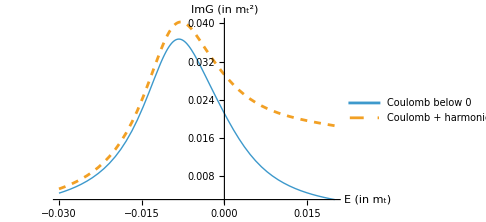

```mathematica
Sum[1/n^3*1/(-En-kappa^2/(mt*n^2)-I*Gammat),{n,1,Infinity}]+xf*Sum[1/(-En+xo*n-I*Gammat),{n,1,20}];
Assuming[kappa>0&&mt>0&&Gammat>0&&En∈Reals,Simplify[Im[%]*kappa^3/(Pi)]];
tmpMyExpression3=Assuming[mt>0,Simplify[%//.{En->xE*mt,Gammat->xΓ*mt,kappa->xKappa*mt}]]
Sum[1/n^3*1/(-En-kappa^2/(mt*n^2)-I*Gammat),{n,1,Infinity}]
Assuming[kappa>0&&mt>0&&Gammat>0&&En∈Reals,Simplify[Im[%]*kappa^3/(Pi)]];
tmpMyExpression4=Assuming[mt>0,Simplify[%//.{En->xE*mt,Gammat->xΓ*mt,kappa->xKappa*mt}]]
Plot[{tmpMyExpression4//.{mt->1,xKappa->inpKappa,xΓ->inpΓ},(tmpMyExpression3)//.{mt->1,xKappa->inpKappa,xΓ->inpΓ,xo->0.002,xf->0.05}},{xE,-0.03,0.02},AxesLabel->{"E (in m_t)","ImG (in m_t^2)"},PlotStyle->{Thick,Dashed},PlotLegends->Placed[{"Coulomb below 0","Coulomb + harmonic"},{0.82,0.7}],PlotRange->Full,ImageSize->Medium]
```

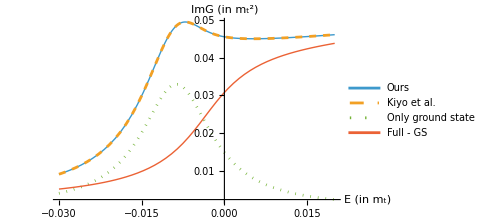

```mathematica
mt^2/(2*Pi)*xKappa*Im[-1/(2*k)+Log[I*xmu/(2*v)]-PolyGamma[1-k]];
tmpKyioEtAlExpression=(%//.{k->I*xKappa/v,v->Sqrt[xE+I*xΓ]});
inpAlphaS=0.14;
inpKappa=4/3*inpAlphaS/2;
inpΓ=1.36/173;
Plot[{tmpMyExpression//.{mt->1,xKappa->inpKappa,xΓ->inpΓ},tmpKyioEtAlExpression//.{mt->1,xKappa->inpKappa,xΓ->inpΓ,xmu->1},tmpMyExpression2//.{mt->1,xKappa->inpKappa,xΓ->inpΓ},(tmpMyExpression-tmpMyExpression2)//.{mt->1,xKappa->inpKappa,xΓ->inpΓ}},{xE,-0.03,0.02},AxesLabel->{"E (in m_t)","ImG (in m_t^2)"},PlotStyle->{Thick,Dashed,Dotted,Thick},PlotLegends->Placed[{"Ours","Kiyo et al.","Only ground\nstate","Full - GS"},{0.82,0.7}],PlotRange->Full,ImageSize->Medium]
```

```mathematica
tmpKyioEtAlExpression//.{mt->1,xKappa->inpKappa,xΓ->inpΓ}
```

0.0148545 (Im[Log[(ⅈ xmu)/(2 √((0.+0.00786127 ⅈ)+xE))]-PolyGamma[0,1-(ⅈ xkappa)/(√((0.+0.00786127 ⅈ)+xE))]]+1/2 Re[(√((0.+0.00786127 ⅈ)+xE))/xkappa])

```mathematica
mt^2/(2*Pi)*xKappa*Im[-1/(2*k)+Log[I*xmu/(2*v)]-PolyGamma[1-k]];
tmpKyioEtAlExpression=(%//.{k->I*xKappa/v,v->Sqrt[xE+I*xΓ]});
inpAlphaS=0.14;
inpKappa=4/3*inpAlphaS/2;
inpΓ=1.36/173;
Plot[{tmpMyExpression//.{mt->1,xKappa->inpKappa,xΓ->inpΓ},tmpKyioEtAlExpression//.{mt->1,xKappa->inpKappa,xΓ->inpΓ,xmu->1},tmpMyExpression2//.{mt->1,xKappa->inpKappa,xΓ->inpΓ},(tmpMyExpression-tmpMyExpression2)//.{mt->1,xKappa->inpKappa,xΓ->inpΓ}},{xE,-0.03,0.02},AxesLabel->{"E (in m_t)","ImG (in m_t^2)"},PlotStyle->{Thick,Dashed,Dotted,Thick},PlotLegends->Placed[{"Ours","Kiyo et al.","Only ground\nstate","Full - GS"},{0.82,0.7}],PlotRange->Full,ImageSize->Medium]
```

```mathematica
Sum[1/n^3,{n,1,Infinity}]
```

Zeta[3]

```mathematica
64*8
```

512

```mathematica
(0.18^2/172.5/2)^(1/3)
```

0.0454543

```mathematica
DoubleFa
```

```mathematica
Gamma[2]
```

1

```mathematica
6.5!!
```

70.4068

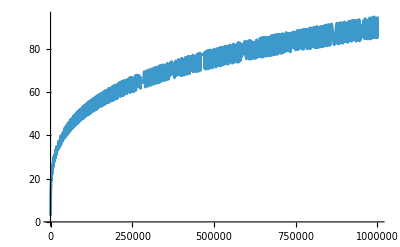

```mathematica
Plot[LaguerreL[1/2,x,0]*Sqrt[2^(x+3)*x!/(2x+1)!!],{x,0,1000000}]
```